```mathematica
k = {k1, k2};
n1 = {(√3)/2, 3/2};
n2 = {(-√3)/2, 3/2};
```

```mathematica
f = 2 (Jx Exp[I k.n1]+ Jy Exp[I k.n2] + Jz)
```

2 (ⅇ^(ⅈ ((√3 k1)/2+(3 k2)/2)) Jx+ⅇ^(ⅈ (-(√3 k1)/2+(3 k2)/2)) Jy+Jz)

```mathematica
Conjf = 2 (Jx Exp[-I k.n1]+ Jy Exp[-I k.n2] + Jz)
```

2 (ⅇ^(-ⅈ ((√3 k1)/2+(3 k2)/2)) Jx+ⅇ^(-ⅈ (-(√3 k1)/2+(3 k2)/2)) Jy+Jz)

```mathematica
H= {{0, I f},{- I Conjf, 0}};
```

```mathematica
Eigenvalues[H] //FullSimplify
```

{2 ⅇ^(-1/4 ⅈ (2 √3 k1+3 k2)) √(ⅇ^(1/2 ⅈ (2 √3 k1+3 k2)) (Jx^2+Jy^2+Jz^2+2 Jx Jy Cos[√3 k1]+2 Jy Jz Cos[1/2 (√3 k1-3 k2)]+2 Jx Jz Cos[1/2 (√3 k1+3 k2)])),-2 ⅇ^(-1/4 ⅈ (2 √3 k1+3 k2)) √(ⅇ^(1/2 ⅈ (2 √3 k1+3 k2)) (Jx^2+Jy^2+Jz^2+2 Jx Jy Cos[√3 k1]+2 Jy Jz Cos[1/2 (√3 k1-3 k2)]+2 Jx Jz Cos[1/2 (√3 k1+3 k2)]))}

```mathematica
λ [Jx_, Jy_, Jz_, {k1_, k2_}] = 2 ⅇ^(-1/4 ⅈ (2 √3 k1+3 k2)) √(ⅇ^(1/2 ⅈ (2 √3 k1+3 k2)) (Jx^2+Jy^2+Jz^2+2 Jx Jy Cos[√3 k1]+2 Jy Jz Cos[1/2 (√3 k1-3 k2)]+2 Jx Jz Cos[1/2 (√3 k1+3 k2)]))
```

2 ⅇ^(-1/4 ⅈ (2 √3 k1+3 k2)) √(ⅇ^(1/2 ⅈ (2 √3 k1+3 k2)) (Jx^2+Jy^2+Jz^2+2 Jx Jy Cos[√3 k1]+2 Jy Jz Cos[1/2 (√3 k1-3 k2)]+2 Jx Jz Cos[1/2 (√3 k1+3 k2)]))

```mathematica
BrZone = Polygon[{{ 2 π/(√3), 0}, {π/(√3), π },{ -π/(√3), π },{-2 π/(√3),0}, { -π/(√3), -π},{π/(√3), -π}}]
```

Polygon[…]

Это изотропный случай, когда J_x = J_y = J_z = 1

```mathematica
Plot3D[Abs[λ[1, 1, 1, {k1, k2}]], {k1, k2} ∈ BrZone]
```

-Graphics3D-

J_x =  J_y = 0.6, J_z = 1.8

```mathematica
Plot3D[{Abs[λ[0.6, 0.6, 1.8, {k1,k2}]]}, {k1, k2} ∈ BrZone ]
```

-Graphics3D-

J_x =  J_y = 1.2, J_z = 0.6

```mathematica
Plot3D[{Abs[λ[1.2, 1.2, 0.6, {k1, k2}]]}, {k1, k2} ∈ BrZone ]
```

-Graphics3D-

Базисные векторы обратной решетки:

```mathematica
b1 = 4 π/(√3){(√3)/2, 1/2};
b2 = 4 π/(√3){-(√3)/2, 1/2};
```

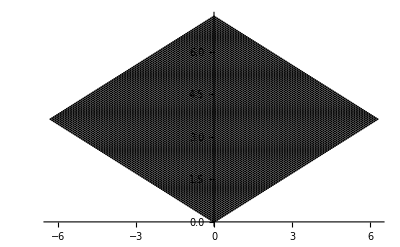

```mathematica
ListPlot[Table[1/100 4 π/(√3)({{(√3)/2, (-√3)/2}, {1/2, 1/2}}).{n,m}, {n, 0, 100}, {m, 0, 100}], PlotStyle->Black]
```

```mathematica
A = ParallelTable[N[1/100 4 π/(√3)({{(√3)/2, (-√3)/2}, {1/2, 1/2}}).{n,m}], {n, 0, 1000}, {m, 0, 1000}];
Dimensions[A]
```

{1001,1001,2}

Строим плотность состояний для изотропного случая, когда J_x = J_y = J_z = 1

```mathematica
Energies = Flatten[ParallelTable[N[Abs[λ[1,1,1,A[[n,m]]]]],{n,1,1001},{m,1,1001}]];
```

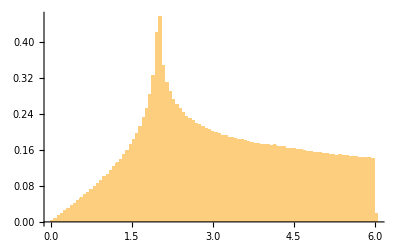

```mathematica
Histogram[Energies, {"Raw", 100}, PDF]
```

Строим для случая с щелью, когда J_x =  J_y = 0.6, J_z = 1.8

```mathematica
Energies1 = Flatten[ParallelTable[N[Abs[λ[0.6,0.6,1.8,A[[n,m]]]]],{n,1,1001},{m,1,1001}]];
```

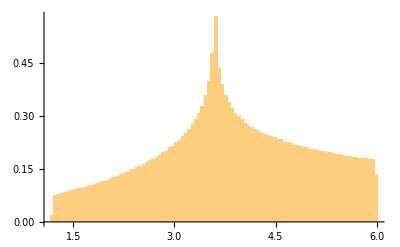

```mathematica
Histogram[Energies1, {"Raw", 100}, PDF]
```

Теперь рассмотрим случай, где два пика, J_x =  J_y = 1.2, J_z = 0.6

```mathematica
Energies2 = Flatten[ParallelTable[N[Abs[λ[1.2,1.2,0.6,A[[n,m]]]]],{n,1,1001},{m,1,1001}]];
```

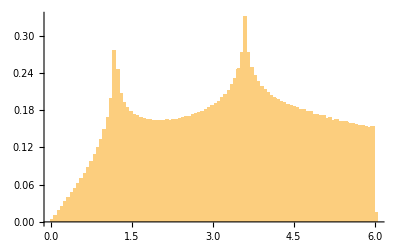

```mathematica
Histogram[Energies2, {"Raw", 100}, PDF]
```